# Ballistic Pendulum

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 10/23/2024

## Purpose

To understand the conservation of energy and momentum.

## Readings

You can explore these concepts using Wikipedia or yous favorite mechanics textbook,
Propagation of uncertainty (partial derivatives), Conservation of Energy,  Conservation of momentum,  Elastic collision, Inelastic collision, Kinematics, kinematics equations.

Use these simulations to get familiar with the lab,
Ballistic Pendulum
Projectile Motion

And review the Error Propagation chapter from Taylor’s book.

### Theory and concepts in short

In the absence of external forces momentum of a system is conserved. In the two body collision the total momentum of the system before and after the collision are given by
-Graphics-
where the subscripts “i” and “f” stand for “initial” and “final.”
Mechanical energy is the sum of kinetic and potential energies. The law of conservation of energy states that the total energy of a system is always conserved. However, unlike momentum and total energy, kinetic energy is not usually conserved.  A collision in which kinetic energy is conserved is an elastic collision. In an inelastic collision some of the kinetic energy is converted into non-mechanical energy (often heat). Total energy is still conserved, but mechanical energy is not. Inelastic collisions in which two bodies stick together (sometimes called perfectly inelastic collisions) have a maximum loss of kinetic energy.

### An example for error propagation

You have measured various quantities y and h with uncertainties Δy and Δh. Now you want to use these measurement to calculate a quantity x which is a function of your measured quantities,
x = f(y,h).
The uncertainty in x is then given by,
Δx = √(((∂f)/(∂y)Δy)^2 + ((∂f)/(∂h)Δh)^2),
where (∂f)/(∂y)is the partial derivative of f with respect to y. All that is meant by the term partial derivative with respect to y is that ignore that h is a variable and just take the regular derivative df/dy.

## Dialog:

In this experiment you will use the principles of conservation of momentum and energy to determine the range of a horizontally projected ball with an estimate of error in your prediction. You will then measure the distance the ball actually travels, determine the error in your measurement, and compare the predicted and experimental ranges to see if they agree.

Warning! 
- Treat the spring-loaded gun with great caution. 
- Load or cock the apparatus only just prior to firing.
- No one should ever be in front of a loaded gun.
- Warn others when you are ready to make a shot.
- Watch your fingers.

### Step 1. Ballistic Pendulum (Measurements)

In this part you shoot a steel ball of mass m from a spring-loaded gun into a catcher-swing of mass M. The ball has an initial velocity of v. The catcher is initially at rest and is free to swing like a pendulum. After capturing the ball, the catcher+ball have a velocity V. As shown in Figure 1, the catcher with the ball continues to swing upward until it stops with its center of mass at a vertical distance, h, above the starting level. A ratchet arrangement keeps the pendulum from falling back after it reaches its highest latch as the catcher swing upward.
-Graphics-
- When cocking the spring plunger push straight back so as not to bend the rod.
- Careful! There are several catches on the plunger; always use the same catch. 
- Shoot the ball into the catcher and measure the vertical rise h (measure to mark on catcher arm showing center if mass of combined system of catcher+ball).
- Repeat at least five times. Calculate h̄, the average of your measurements, and the standard deviation, σ_h.
- The mass (M) of the catcher, is given to you on the body of the apparatus. 
- Measure the mass m of the ball using the scale. 
- Use a meter stick to measure the vertical distance y through which the ball will fall while in flight.
- To get Δy, the error in y, you will simply estimate how accurate your measurement is.
- Record your measurement, and their error with correct significant digits in the table below.

```mathematica
h={0.140-0.04,0.138-0.04,0.138-0.04,0.140-0.04,0.140-0.04}
 h̄=Mean[h]
Δh=StandardDeviation[h]
M=0.200 (*kg*)
m=0.0578 (*kg*)
Grid[{{Text["Ballistic Pendulum and Height"],SpanFromLeft},{"m, kg","M, kg","h̄±σ_h, m"},{m,M, NumberForm[h̄ ,{3,3}]± NumberForm[Δh,{3,5}]}},Frame->All]
```

{0.1,0.098,0.098,0.1,0.1}

0.0992

0.00109545

0.2

0.0578

Ballistic Pendulum and Height |  | 
m, kg | M, kg | h̄±σ_h, m
0.0578 | 0.2 | 0.099±0.00110

### Step 2. Projectile Motion (Measurements)

In this part the spring-loaded gun is used to fire the ball horizontally from an initial elevation y with initial velocity v. The ball hits the floor at a distance x as shown in Figure 2. 
-Graphics-
-Tape a large sheet of paper to the floor to where a test shot landed.
- Measure the range of the ball x for at least five trials.
- Calculate x̄, the average of your measurements, and the standard deviation, σ_x. You will compare the predicted (theoretical values) with your measurements in this part.

```mathematica
x={2.66,2.67,2.48,2.59,2.57}
 x̄=Mean[x]
Δx=StandardDeviation[x]
PlusMinus[N[Mean[x]],N[StandardDeviation[x]]]
```

{2.66,2.67,2.48,2.59,2.57}

2.594

0.0770065

2.594±0.0770065

### Step 3. Theory & Results

- Use the rules of conservation of energy and momentum in the ballistic pendulum experiment,  to find an expression for the v, the initial velocity of the steel ball, as a function of m, M, and h.
- In the  projectile motion, find an expression for x, the range of the steel ball as a function of v, and y.
- Since the ball is shot from the same apparatus, we can assume that v, the initial velocity of the ball, is the same in both parts of the experiment. Combine the expressions you found in the last two steps to find x, the range of the steel ball as a function of m, M, h, and y.
- Use the rule of error propagation to calculate the uncertainty in x from uncertainties of y and h. You can ignore the uncertainties of m and M since they are small. 
- Plot PDF of predicted and measured distance.

--Ballistic pendulum--
v1^2 - 0 = 2gh
⇒v1 = Sqrt(2gh)
v0m = v1(m+M)
⇒ v0 = Sqrt(2gh)*(m+M)/m

--Projectile Motion--
y =(0t+) gt^2/2
⇒t = Sqrt(2y/g)

x=v_xt = v0 * Sqrt(2y/g) = Sqrt(2gh)*(m+M)/m * Sqrt(2y/g) = 2(m+M)*Sqrt(hy)/m

```mathematica
y = 0.769 ;(*m*)
dely =0.001;
m  ;(*kg*)
M;
v = Sqrt[(2*9.81*h̄)] * (m+M)/m ;(* h has 3 sigfigs, hence so does v*)
delh = Δh;
delv = (delh/2);
xPred = 2(m+M)*Sqrt[h̄*y]/m
delxPred = Sqrt[(h̄*(m+M)*dely/(m*Sqrt[h̄*y]))^2+(y*(m+M)*delh/(m*Sqrt[h̄*y]))^2]
(*Δx=√(((∂f)/(∂y)Δy)^2 + ((∂f)/(∂h)Δh)^2)*)
```

2.46379

0.0136976

- Record your results in the table below.

```mathematica
Grid[{{Text["Results Table"],SpanFromLeft},{"m, kg","M, kg","h±Δh, m","y±Δy, m", "Predicted x±Δx, m","Measured x±Δx, m"},{m,M,NumberForm[h̄ ,{3,3}]± NumberForm[Δh,{3,5}],NumberForm[y,{3,3}]± NumberForm[dely,{3,5}],NumberForm[xPred,3]± NumberForm[delxPred,3],NumberForm[ x̄,3]± NumberForm[Δx,{3,4}]}},Frame->All]
```

Results Table |  |  |  |  | 
m, kg | M, kg | h±Δh, m | y±Δy, m | Predicted x±Δx, m | Measured x±Δx, m
0.0578 | 0.2 | 0.099±0.00110 | 0.769±0.00100 | 2.46±0.0137 | 2.59±0.0770

- Plot the normal distribution functions for measured and predicted values of x in one figure. Explain how well your measured and predicted values of x agree from the overlap of the normal distributions.

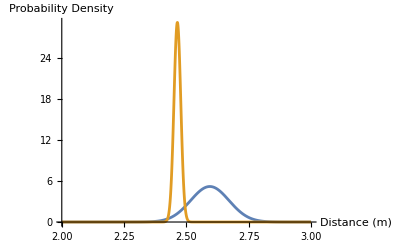

```mathematica
Plot[{PDF[NormalDistribution[x̄,Δx],xa],PDF[NormalDistribution[xPred,delxPred],xa]},{xa,2,3},PlotRange->All, AxesLabel->{"Distance (m)","Probability Density"}]
```

```mathematica
x̄ (*To the right*);
xPred (*To the left*);
x̄-2Δx
xPred+delxPred
```

2.43999

2.47749

Rutgers 275 Classical Physics Lab
“Ballistic Pendulum”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014